# Analizador de datos

## Inicialización

```mathematica
(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 400;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
path = FileNameJoin[{$HomeDirectory,"HuertosLog"}];
SetDirectory[path];
```

## Contadores de experimentos y rondas

```mathematica
GetNumberOfExperiments[]:=Module[{x},
Max[Map[First[StringCases[#,"Experimento_"~~x_~~_:>ToExpression[x]]]&,FileNames[]]]
];
GetNumberOfRounds[experiment_]:=Module[{expString,rounds,x},
expString = "Experimento_"<>ToString[experiment]<>"_Ronda_";
rounds = Map[First[StringCases[#,expString~~x_:>ToExpression[x]]]&,FileNames[]];
Max[rounds]
];
GetNumberOfFruits[experiment_,round_,player_]:=Module[{pathStr,filesInPath,pattExpr,fruits},
pathStr = "Experimento_"<>ToString[experiment]<>"_Ronda_"<>ToString[round];
filesInPath = Map[FileBaseName,FileNames[All,pathStr]];
pattExpr = "fruit_"<>player<>"_";
fruits = DeleteCases[Map[StringCases[#,pattExpr~~x_:>ToExpression[x]]&,filesInPath],{}];
Max[Flatten[fruits]]
];
```

```mathematica
GetNumberOfFruits[1,1,"PlayerB"]
```

1

```mathematica
GetNumberOfRounds[1]
```

3

```mathematica
GetNumberOfExperiments[]
```

1

## Graficador de ruta de cursores

```mathematica
PositionParse[position_String]:=Map[ToExpression,StringSplit[StringTake[position,{2,-2}],","]];
GetCursorData[experiment_,round_,cursor_]:=Block[{path,rawData,dated,numericPosition,formatted},
path = "Experimento_"<>ToString[experiment]<>"_Ronda_"<>ToString[round];
rawData = Drop[Import[FileNameJoin[{path,"cursordata_"<>cursor<>".csv"}]],1];
dated = MapAt[DateObject,rawData,{All,1}];
numericPosition = MapAt[PositionParse,dated,{All,2}];
formatted = Map[Association[Thread[{"Date","Position","Selecting","Access"}->#]]&,numericPosition];
Dataset[formatted]
];
PlotCursorPaths[experiment_,round_]:=Block[{cursorAPos,cursorBPos},
cursorAPos = Normal[GetCursorData[experiment,round,"CursorA"][All,"Position"]];
cursorBPos = Normal[GetCursorData[experiment,round,"CursorB"][All,"Position"]];
ListLinePlot[
{cursorAPos,cursorBPos},
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["X",bigFontSize], Style["Y",bigFontSize]}, 
ImageSize->plotSize,
BaseStyle->FontSize->smallFontSize,
GridLinesStyle->{Directive[Black,Thick,Dashed],Directive[Thin,Black]},
PlotLegends->Placed[LineLegend[{"Cursor A","Cursor B"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&)],{Right,Bottom}],
PlotMarkers->None,
PlotRangePadding->Automatic,
PlotStyle->colors,
Frame->True,
AspectRatio->1
]
];
```

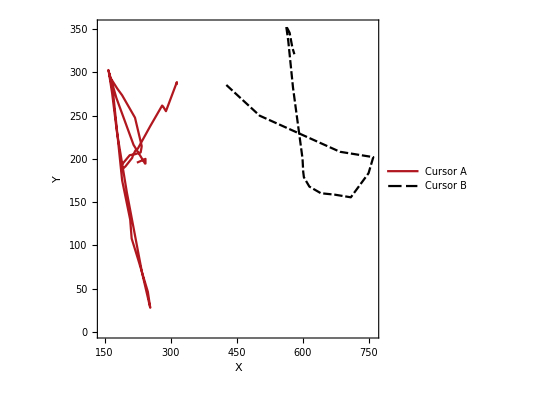
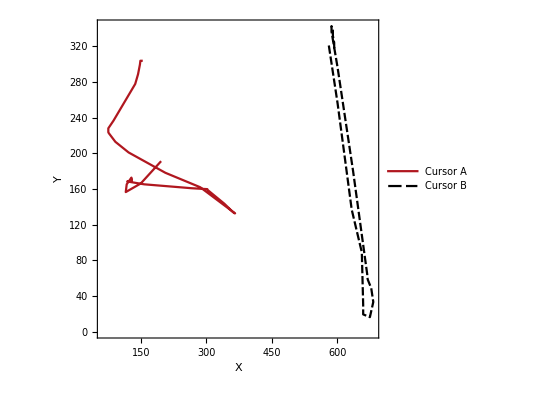
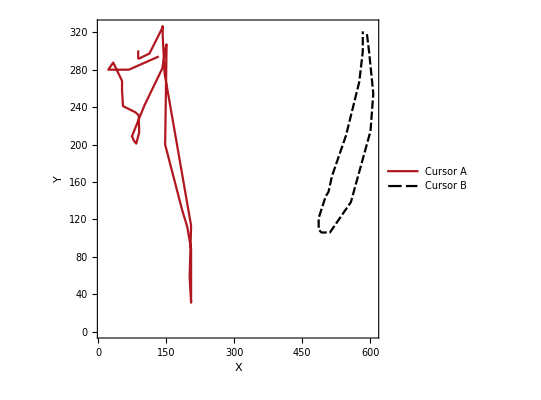

```mathematica
Table[PlotCursorPaths[1,r],{r,1,3,1}]
```